1)  set J and calc. (N̂)_ij^J and (Ĥ)_ij^J                      untainted/*.exe  boundstate with INQUA_N as in RHS calc.
2)

```mathematica
jj =0;
pi="-";
```

Setup of the RHS of the LIT equation  (Η̂-B_deu-σ_r-iσ_i) Ψ_LIT=Ô Ψ_deu  (which is a vector!)

Setup of the LHS of the LIT equation  (Η̂-B_deu-σ_r-iσ_i) Ψ_LIT=Ô Ψ_deu  

Read Norm  ( (Ν^J)_(l_n l_m))  and Hamilton  ( (Η^J)_(l_n l_m))  Matrix dimensionality for  J={0: N_1
1: N_0+N_1+N_2
2: N_1+N_2+N_3

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.00616034+2.42265×10^-6 ⅈ,0.00834653+5.9485×10^-6 ⅈ,0.00715923+8.21×10^-6 ⅈ,0.00400344+0.000010711 ⅈ,0.00218502+0.0000117525 ⅈ,0.00106199+0.0000123275 ⅈ,0.000511117+0.0000125955 ⅈ,0.000070913+0.000012804 ⅈ,-0.000259647+0.000012957 ⅈ,-0.000621173+0.000013122 ⅈ,«9»,-0.00193965+0.0000136995 ⅈ,-0.00194225+0.0000137005 ⅈ,-0.00194515+0.000013702 ⅈ,-0.00194765+0.000013703 ⅈ,-0.00194825+0.0000137035 ⅈ,-0.00194945+0.000013704 ⅈ,-0.00194995+0.000013704 ⅈ,-0.00195015+0.000013704 ⅈ,-0.00195055+0.000013704 ⅈ,-0.00195065+0.0000137045 ⅈ},«27»,{-0.00195065+«24» ⅈ,«27»,-«12»+«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.00615986+2.42265×10^-6 ⅈ,0.00834535+5.9485×10^-6 ⅈ,0.00715761+8.21×10^-6 ⅈ,0.00400132+0.000010711 ⅈ,0.0021827+0.0000117525 ⅈ,0.00105955+0.0000123275 ⅈ,0.000508623+0.0000125955 ⅈ,0.0000683778+0.000012804 ⅈ,-0.000262212+0.000012957 ⅈ,-0.000623771+0.000013122 ⅈ,«9»,-0.00194236+0.0000136995 ⅈ,-0.00194497+0.0000137005 ⅈ,-0.00194787+0.000013702 ⅈ,-0.00195037+0.000013703 ⅈ,-0.00195097+0.0000137035 ⅈ,-0.00195217+0.000013704 ⅈ,-0.00195267+0.000013704 ⅈ,-0.00195287+0.000013704 ⅈ,-0.00195327+0.000013704 ⅈ,-0.00195337+0.0000137045 ⅈ},«27»,{«1»}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Append[LIToverlap,{{1,1.28296×10^-6-2.56948×10^-21 ⅈ},{199/100,1.41232×10^-6+1.15826×10^-21 ⅈ},{149/50,1.49006×10^-6+1.23426×10^-21 ⅈ},{397/100,1.50831×10^-6-2.54306×10^-21 ⅈ},{124/25,1.47183×10^-6+8.08145×10^-21 ⅈ},{119/20,1.39299×10^-6+1.34023×10^-20 ⅈ},{347/50,1.28717×10^-6-4.67342×10^-21 ⅈ},«37»,{1114/25,4.97356×10^-8+8.61533×10^-22 ⅈ},{911/20,4.63622×10^-8-9.00441×10^-22 ⅈ},{2327/50,4.35439×10^-8+1.29044×10^-21 ⅈ},{4753/100,4.1202×10^-8-6.15839×10^-22 ⅈ},{1213/25,3.92836×10^-8+5.68932×10^-22 ⅈ},{4951/100,3.77584×10^-8+2.06511×10^-22 ⅈ},«49»}].

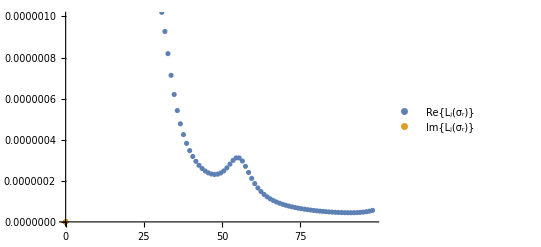

```mathematica
momentum=1;
sigmaI=5;
smin=1;smax=100;nbrs=100;
sigmaRange=Range[smin,smax,(smax-smin)/nbrs];

file="/home_th/kirscher/kette_repo/sim_par/nucleus/2n/LIT_prep/beyond_siegert/av18_deuteron/norm-ham-litME-"<>ToString[jj]<>pi;
NormHamMat=ReadList[file,Number];
JbasisDim=NormHamMat[[1]];
norm=ArrayReshape[NormHamMat[[2;;JbasisDim^2+1]],{JbasisDim,JbasisDim}];
ham=ArrayReshape[NormHamMat[[JbasisDim^2+2;;2 JbasisDim^2+1]],{JbasisDim,JbasisDim}];
file="/home_th/kirscher/kette_repo/sim_par/nucleus/2n/LIT_prep/beyond_siegert/av18_deuteron/LIT_SOURCE-"<>ToString[jj]<>pi;
RHS=ReadList[file,Real,RecordLists->True];
(*Dimensions[norm];
Dimensions[ham];*)
SlitDim=Dimensions[RHS[[1]]][[1]];
If[(JbasisDim==SlitDim-1)==False,
Print["Dim(Norm/H) ≠ Dim(S_LIT)"];
Print["Dim(Norm/H) = "<>ToString[JbasisDim]];
Print["Dim(S_LIT)   = "<>ToString[SlitDim]];
];
inhomo=RHS[[momentum]][[2;;]];
lOfSigma={};
For[n=1,n<nbrs,n++,(
(*Subscript[σ, r]=n;Subscript[σ, i]=5;σ=Subscript[σ, r]+I Subscript[σ, i];*)
coeff=LinearSolve[ham-Conjugate[sigmaRange[[n]]+sigmaI I] norm,inhomo];
lOfSigma=Append[lOfSigma,{sigmaRange[[n]],Conjugate[coeff].norm.coeff}];
)];
LIToverlap=Append[LIToverlap,lOfSigma];
lOfSigma;
ListPlot[{Re[lOfSigma],Im[lOfSigma]},PlotLegends->{"Re{L_j(σ_r)}","Im{L_j(σ_r)}"},PlotRange->{0,10^(-6)}]
```

```mathematica
ϕ=Pi/3;
θ=Pi/3;
Plot[Re[expandedState[r Cos[θ] Sin[ϕ],r Sin[θ] Sin[ϕ],r Cos[ϕ],Lsets[[jj+1]],basisWidths,coeff]],{r,.01,6.5}]
```

```mathematica
basisWidths//MatrixForm
```

({12.9567,5.13467,2.939,1.69017,0.843,0.257369,0.13852,0.038519}
{0.444741,2.939,1.69017,1.18524,0.843,0.50011}
{0.444741,2.939,1.69017,1.18524,0.843,0.50011}
{0.444741,2.939,1.69017,1.18524,0.843,0.50011})

```mathematica
normmalcoeff=norm.coeff
normmalcoeff.coeff//MatrixForm
Conjugate[coeff].norm.coeff
```

{1.05785×10^-6+3.06049×10^-8 ⅈ,2.41402×10^-8+7.40847×10^-10 ⅈ,8.60316×10^-8+2.53363×10^-9 ⅈ,1.86044×10^-7+5.42301×10^-9 ⅈ,3.68715×10^-7+1.07022×10^-8 ⅈ,8.94637×10^-7+2.58962×10^-8 ⅈ}

1.36588×10^-12+7.91869×10^-14 ⅈ

1.36817×10^-12-1.31266×10^-27 ⅈ

```mathematica
ell=1;
m1=4;
m2=4;
(2 ell+1)!!/(2^(2+ell) (basisWidths[[ell+1]][[m1]]+basisWidths[[ell+1]][[m2]])^(1+ell)) Sqrt[Pi/(basisWidths[[ell+1]][[m1]]+basisWidths[[ell+1]][[m2]])]
```

0.0768279